# Transient weak gravity in scalar-tensor theories

## Chapter 1: Introduction

This is the Mathematica implementation of the conformal-coupling model (a special case of the disformal-coupling model) as presented in the article Transient weak gravity in scalar-tensor theories by M. Wittner, G. Laverda, O. Piattella, L. Amendola. We consider a universe constituted only of matter and dark energy, the latter described by a dynamical scalar field. In general, both species are coupled disformally trough two coupling functions: D(ϕ) pure disformal transformation and C(ϕ) pure conformal transformation. We will consider only the pure conformally-coupled version (i.e. D(ϕ)=0) in this notebook. 

The notebook is divided as follows: in the first chapter we will define the most important quantities that enter the computations and the value of the cosmological parameters (such as the present-day values of the density functions Ω). In the second chapter, the background equations of motion are solved via a shooting method. The solutions are obtained for five different types of coupling (four conformally-coupled scenarios and one uncoupled scenario). In the third chapter, the perturbation equations are solved both in their exact form and in their quasi-static-approximated form. Various plotting sections are inserted in every chapter.

We will adopt the following choices as the basis of our method of analysis:

	- The independent time-variable is n=ln(a), where a is the scale-factor. The intervals on which the solutions are defined are -4<n<0 for the 	background solutions and -2.5<n<0 for the perturbation solutions.
	
	- All quantities are considered to be dimensionless, as explained in the article.
	
	- The conformal Hubble function is normalised to be ℋ=1 at the present time.
	
	- Four versions of the conformal-coupling model are considered, i.e. four different values of the coupling parameter β_c are included. In total 	we will study the following cases: β_c=(m_c)^(-2)=4, 3, 2.5, 2, the uncoupled case β_c=0 and the ΛCDM case.

The full evaluation of the notebook takes around 3 minutes on an average laptop.

The use of this notebook is free provided that the article Transient weak gravity in scalar-tensor theories (arXiv:2003.08950) and its authors M. Wittner, G. Laverda, O. Piattella, L. Amendola are cited.

This notebook has been created by Giorgio Laverda in collaboration with M. Wittner, O. Piattella and L. Amendola.

## Parameters and free functions

This section defines a bunch of constants, free functions, parameters and other things later used in the computations. We also define the two matrices bgtot and perttot that will contain the solutions to the background equations and the perturbation equations respectively. As a quick reference, we summarise pairs model-index in the following table. Both matrices adopt the same convention.

	Index i | Model
1 | ΛCDM
2 | uncoupled  βc=0
3 | conformal coupling βc=4
4 | conformal coupling βc=3
5 | conformal coupling βc=2.5
6 | conformal coupling βc=2

```mathematica
(* Cosmological density parameters at the present time *)
Subscript[Ω0, m]=(260 +49)/1000; (*dark matter*)
Subscript[Ω0, ϕ]=1.-Subscript[Ω0, m] ;(*dark energy*)

(* Extrema of the solution interval (in e-folds) *)
ni=-4.;
nf=0.; (* present *)

(* Coupling parameters *)
βcb1=4;
βcb2=3;
βcb3=25/10;
βcb4=2;

(* Potential for the scalar field ϕ (plus cosmological constant) *)
v[n_]:=1/2mv[n]^2*ϕ[n]^2 + v0 

(* Conformal Hubble function *) 
ℋ[n_]:=Sqrt[(Exp[2n])/3.*(Subscript[ρ, m][n] + v[n]) / (1. - 1./6.*ϕ'[n]^2) ];
ξ[n_]:=ℋ'[n]/ℋ[n];

(* Dark energy density *)
Subscript[ρ, ϕ][n_]:=(1./2.)*(ℋ[n]*Exp[-n])^2*ϕ'[n]^2 + v[n]

(* Creating matrices that will contain all results *)
bgtot=ConstantArray[0,{15,20}]; (* background solutions *)
perttot=ConstantArray[0,{15,20}]; (* perturbation solutions *)

(* colours used in plots *)
col=ColorData["Rainbow"];
col4=col[.99];
col3=col[.7];
col2=col[.4];
col1=col[.1];
col5=col[.85];
col6=col[.55];
col7=col[.25];
col8=col[.01];
```

## Chapter 2: Background differential equations

We are ready to solve the two differential equations for the coupled species. We are using a shooting method that will yield the best value of m_vto fit the current cosmological densities. The boundary conditions are set to match the present-day values of the cosmological densities. A loop will take care of computing the background solutions for all the models defined by the choice of parameters in the previous section. 

The loop contains an “output check” part that can be uncommented to visualise the values at the extrema of the interval of various functions and variables.

## Solutions of the differential equations

```mathematica
(* ΛCDM background solution *)
bgtot[[1,1]]=0;
bgtot[[1,2]]=0;
bgtot[[1,3]]=3*Subscript[Ω0, m]*Exp[-3n];
bgtot[[1,4]]=0;
bgtot[[1,5]]=0;
bgtot[[1,6]]=0;
bgtot[[1,7]]=0;
bgtot[[1,8]]=Sqrt[Exp[2n]/3*(3*Exp[-3n]*Subscript[Ω0, m] + 3*Subscript[Ω0, ϕ])];
bgtot[[1,9]]=3*Subscript[Ω0, ϕ];
bgtot[[1,10]]=0;
bgtot[[1,11]]=0;
bgtot[[1,12]]=1;

(* initial conditions for the uncoupled model *)
bcuncoup={ϕ[ni]==2.,ϕ'[nf]==0.,Subscript[ρ, m][ni]==(3)*Subscript[Ω0, m]*Exp[-3ni], (*Subscript[ρ, ϕ][ni]==(3)*Subscript[Ω0, ϕ] *)ϕ[nf]==0};

(* initial condition for the conformally-coupled model *)
bcconf1={ϕ[ni]==2,ϕ'[ni]==0., Subscript[ρ, m][ni]==(8500)*Subscript[Ω0, m]*Exp[-3ni], Subscript[ρ, ϕ][ni]==(330)*Subscript[Ω0, ϕ]}; (*β=4, Subscript[ϕ, 0]=2*)
bcconf2={ϕ[ni]==2,ϕ'[ni]==0., Subscript[ρ, m][ni]==(1200)*Subscript[Ω0, m]*Exp[-3ni], Subscript[ρ, ϕ][ni]==(2200)*Subscript[Ω0, ϕ]};(*β=3, Subscript[ϕ, 0]=2*)
bcconf3={ϕ[ni]==2,ϕ'[ni]==0., Subscript[ρ, m][ni]==(445)*Subscript[Ω0, m]*Exp[-3ni], Subscript[ρ, ϕ][ni]==(5550)*Subscript[Ω0, ϕ]}; (*β=2.5, Subscript[ϕ, 0]=2*)
bcconf4={ϕ[ni]==2,ϕ'[ni]==0., Subscript[ρ, m][ni]==(160)*Subscript[Ω0, m]*Exp[-3ni], Subscript[ρ, ϕ][ni]==(10000)*Subscript[Ω0, ϕ]}; (*β=2, Subscript[ϕ, 0]=2*)

boundarycond={1,bcuncoup, bcconf1, bcconf2, bcconf3, bcconf4};

(* Loop that computes the background cosmology for all models *)
Clear[i];
For[i=3, i<7, i++,{
Clear[mv, mvk, mvsol, βc, md, qsol, q, ϕ, d, c];

(* parameter acquisition *)
Which[ 
i==2, {c0=1.;βc=0.;c[n_]:=1.;d[n_]:=0.;q[n_]:=0., v0=3*Subscript[Ω0, ϕ]},
i==3,{c0=1.;βc=βcb1; c[n_]:=c0*Exp[βc*ϕ[n]^2]; d[n_]:=0.;q[n_]:=-βc*ϕ[n];v0=0},
i==4,{c0=1.;βc=βcb2; c[n_]:=c0*Exp[βc*ϕ[n]^2]; d[n_]:=0.;q[n_]:=-βc*ϕ[n];v0=0},
i==5,{c0=1.;βc=βcb3; c[n_]:=c0*Exp[βc*ϕ[n]^2]; d[n_]:=0.;q[n_]:=-βc*ϕ[n];v0=0},
i==6,{c0=1.;βc=βcb4; c[n_]:=c0*Exp[βc*ϕ[n]^2]; d[n_]:=0.;q[n_]:=-βc*ϕ[n];v0=0}
];

(* differential equations *)
(* conservation equation for matter *)
consmeq= Subscript[ρ, m]'[n] + 3.*Subscript[ρ, m][n] +q[n]*Subscript[ρ, m][n]*ϕ'[n]==0;

 (* klein-gordon equation for the scalar field *) 
kgeq= ϕ''[n]+(2.+ξ[n])*ϕ'[n]+ Exp[2n]* D[v[n], ϕ[n]]*ℋ[n]^(-2) == q[n]*Subscript[ρ, m][n]*Exp[2n]*ℋ[n]^(-2); 

(* equation for the free parameter Subscript[m, v] (Subscript[m, v] is constant) *)
mveq=mv'[n]==0.;

eq={consmeq, kgeq,mveq};

(* numerical solution *)
If[
i==2,{backgroundsol=NDSolve[{eq,boundarycond[[i]]},{ϕ, ϕ', Subscript[ρ, m], mv},{n, ni,nf},Method->{"Shooting","StartingInitialConditions"->{mv[nf]==5, ϕ[nf]==0. ϕ'[nf]==0}}, WorkingPrecision->MachinePrecision]} (* Uncoupled case *),

{backgroundsol=NDSolve[{eq,boundarycond[[i]]},{ϕ, ϕ', Subscript[ρ, m], mv},{n, ni,nf},Method->{"Shooting","StartingInitialConditions"->{mv[ni]==0.01}}, WorkingPrecision->MachinePrecision]} (* Conformal cases *)];


(* extracting the solutions *)
Subscript[ϕ, s][n_]=ϕ[n]/.backgroundsol[[1]];
Subscript[dϕ, s][n_]=ϕ'[n]/.backgroundsol[[1]];
Subscript[ρs, m][n_]=Subscript[ρ, m][n]/.backgroundsol[[1]];
mvs[n_]=mv[n]/.backgroundsol[[1]];
mvk=mvs[0];

Which[ i==2, {dsol[n_]:=0;csol[n_]:=c0*Exp[βc*Subscript[ϕ, s][n]];qsol[n_]:=0.},
		i==3,{dsol[n_]:=0;csol[n_]:=c0*Exp[βc*Subscript[ϕ, s][n]^2];qsol[n_]:=-βc*Subscript[ϕ, s][n]},
		i==4,{dsol[n_]:=0;csol[n_]:=c0*Exp[βc*Subscript[ϕ, s][n]^2];qsol[n_]:=-βc*Subscript[ϕ, s][n]},
		i==5,{dsol[n_]:=0;csol[n_]:=c0*Exp[βc*Subscript[ϕ, s][n]^2];qsol[n_]:=-βc*Subscript[ϕ, s][n]},
		i==6,{dsol[n_]:=0;csol[n_]:=c0*Exp[βc*Subscript[ϕ, s][n]^2];qsol[n_]:=-βc*Subscript[ϕ, s][n]}];

(* recomputing the relevant functions with the previously obtained solutions *)
(* scalar-field potential *)
vsol[n_]:=1/2mvk^2*Subscript[ϕ, s][n]^2+v0;

(* Hubble function *)
ℋsol[n_]:=Sqrt[ (Exp[2n]*(Subscript[ρs, m][n] + vsol[n]))/(3*(1 - (1/6)*Subscript[dϕ, s][n]^2))];

(*dark energy density *)
Subscript[ρs, ϕ][n_]:=1/2*(ℋsol[n]*Exp[-n])^2*Subscript[dϕ, s][n]^2 + vsol[n];

(* ratio between Subscript[ρ, m](a) in the conformal model and its normal bahaviour in ΛCDM *)
x[n_]:=Subscript[ρs, m][n]/(3.*Subscript[Ω0, m]*Exp[-3n]);

(* dark-energy equation of state parameter *)
w[n_]:=(1/2*(ℋsol[n]*Exp[-n])^2*Subscript[dϕ, s][n]^2 - vsol[n])/Subscript[ρs, ϕ][n];

(* controlling the shooting method *)
ρmdiff=(1/3)*Subscript[ρs, m][nf]- Subscript[Ω0, m];
ρphidiff=(1/3)*Subscript[ρs, ϕ][nf]- Subscript[Ω0, ϕ];

(* output check *)
(*
Print["βc = ",βc];
Print["ρm0 = ",Subscript[ρs, m][ni]];
Print["ρϕ0 = ",Subscript[ρs, ϕ][ni]];
Print["Ωm0 = ",1/3*Subscript[ρs, m][ni]*Exp[2ni]/(ℋsol[ni]^2)];
Print["Ωϕ0 = ",1/3*Subscript[ρs, ϕ][ni]*Exp[2ni]/(ℋsol[ni]^2)];
Print["ϕ'[0] = ",Subscript[dϕ, s][0]];
Print["Ωm difference (Ωsol - Ω) = ",ρmdiff];
Print["Ωϕ difference (Ωsol - Ω) = ",ρphidiff];
Print["mv = ",mvs[0]];
Print["|Q(n=0)| = ",Abs[qsol[0]]];  
*)

(* storing the solutions into the solution matrix *)
bgtot[[i,1]]=Subscript[ϕ, s][n]; (* scalar field *)
bgtot[[i,2]]=Subscript[dϕ, s][n];(* first derivative of the scalar field *)
bgtot[[i,3]]=Subscript[ρs, m][n]; (* matter density *)
bgtot[[i,4]]=mvs[n]; (* Subscript[m, v] *)
bgtot[[i,5]]=vsol[n]; (* scalar-field potential *)
bgtot[[i,6]]=csol[n]; (* conformal coupling function C *)
bgtot[[i,7]]=dsol[n]; (* disformal coupling function D (always null) *)
bgtot[[i,8]]=ℋsol[n]; (* conformal Hubble function *)
bgtot[[i,9]]=Subscript[ρs, ϕ][n]; (* scalar-field density *)
bgtot[[i,10]]=qsol[n];(* coupling function Q *)
bgtot[[i,12]]=x[n]; (* ratio matter density over ΛCDM *)
bgtot[[i,13]]=w[n];    (* dark-energy equation of state parameter *)}]
```

## Background cosmology plots

### PLOTS: Matter energy-density ρ_m(a), Dark energy energy-density ρ_ϕ(a)

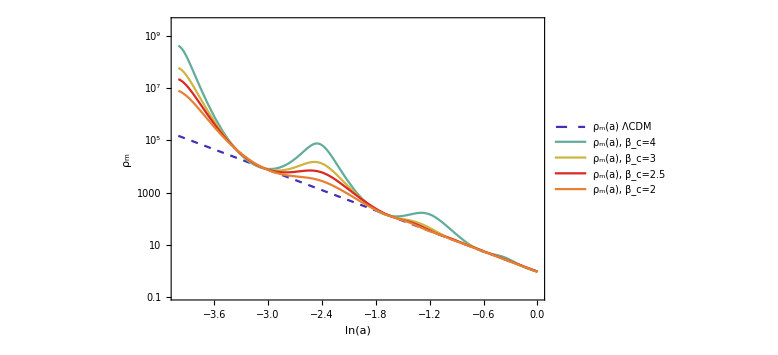

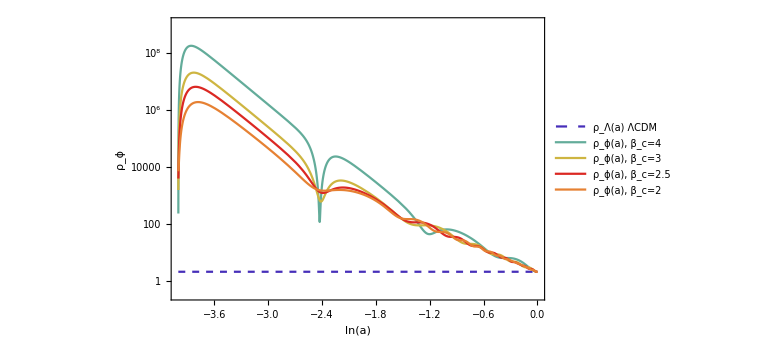

```mathematica
ρplot1=LogPlot[{bgtot[[1,3]],bgtot[[3,3]],bgtot[[4,3]], bgtot[[5,3]], bgtot[[6,3]]}, {n, ni,nf},Frame->True,FrameLabel->{"ln(a)","ρ_m"},PlotStyle->{{col1, Dashed}, {col2},{col3},{col4},{col5}},PlotRange->All,PlotLegends->Placed[LineLegend[{ "ρ_m(a) ΛCDM","ρ_m(a), β_c=4", "ρ_m(a), β_c=3","ρ_m(a), β_c=2.5", "ρ_m(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.82,.75}], GridLines->Automatic,ImageSize->Large]

ρplot2=LogPlot[{bgtot[[1,9]],bgtot[[3,9]], bgtot[[4,9]], bgtot[[5,9]], bgtot[[6,9]]}, {n, ni,nf},Frame->True,FrameLabel->{"ln(a)","ρ_ϕ"},PlotStyle->{{col1, Dashed}, {col2},{col3},{col4},{col5}},PlotRange->All,PlotLegends->Placed[LineLegend[{ "ρ_Λ(a) ΛCDM","ρ_ϕ(a), β_c=4", "ρ_ϕ(a), β_c=3","ρ_ϕ(a), β_c=2.5", "ρ_ϕ(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.82,.75}], GridLines->Automatic,ImageSize->Large]
```

### PLOTS: Dark energy equation of state parameter w_ϕ(a) , effective equation of state parameter w_eff(a)

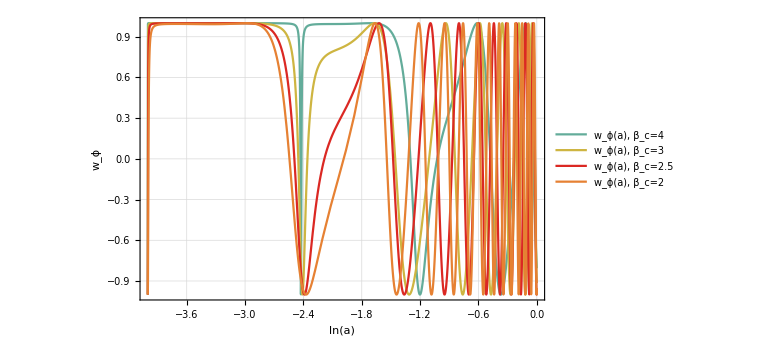

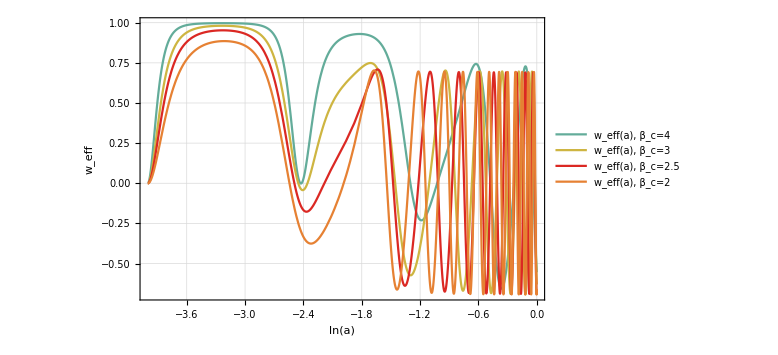

```mathematica
wplot1=Plot[{bgtot[[3,13]],bgtot[[4,13]],bgtot[[5,13]],bgtot[[6,13]]}, {n, ni,nf},Frame->True,FrameLabel->{"ln(a)","w_ϕ"},PlotStyle->{{col2},{col3},{col4},{col5}},PlotRange->All,PlotLegends->Placed[LineLegend[{"w_ϕ(a), β_c=4", "w_ϕ(a), β_c=3","w_ϕ(a), β_c=2.5", "w_ϕ(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.2,.25}], GridLines->Automatic,ImageSize->Large]

weffplot1=Plot[{bgtot[[3,13]]*(bgtot[[3,9]]*Exp[2n])/(3*bgtot[[3,8]]^2),
bgtot[[4,13]]*(bgtot[[4,9]]*Exp[2n])/(3*bgtot[[4,8]]^2),
bgtot[[5,13]]*(bgtot[[5,9]]*Exp[2n])/(3*bgtot[[5,8]]^2),
bgtot[[6,13]]*(bgtot[[6,9]]*Exp[2n])/(3*bgtot[[6,8]]^2)}, {n, ni,nf},Frame->True,FrameLabel->{"ln(a)","w_eff"},PlotStyle->{{col2},{col3},{col4},{col5}},PlotRange->All,PlotLegends->Placed[LineLegend[{"w_eff(a), β_c=4", "w_eff(a), β_c=3","w_eff(a), β_c=2.5", "w_eff(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.2,.25}], GridLines->Automatic,ImageSize->Large]
```

### PLOT: coupling function Q(a)

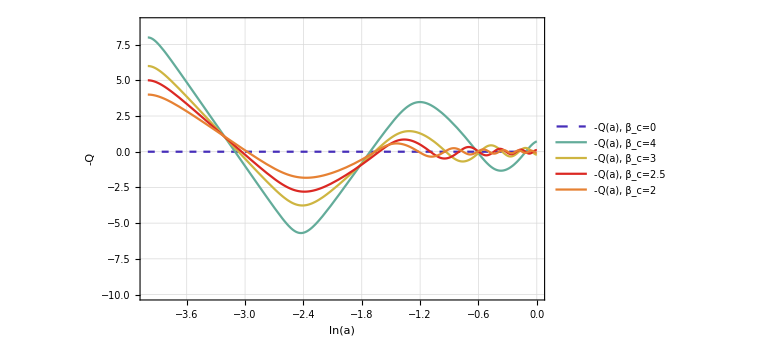

```mathematica
qplot1=Plot[{-bgtot[[2,10]],-bgtot[[3,10]], -bgtot[[4,10]], -bgtot[[5,10]], -bgtot[[6,10]]}, {n, ni,nf},Frame->True,FrameLabel->{"ln(a)","-Q"},PlotStyle->{{col1, Dashed},{col2},{col3},{col4},{col5}},PlotRange->{-10, 9},PlotLegends->Placed[LineLegend[{"-Q(a), β_c=0","-Q(a), β_c=4", "-Q(a), β_c=3","-Q(a), β_c=2.5", "-Q(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.83,.23}], GridLines->Automatic,ImageSize->Large]
```

### PLOT: density functions Ω_m(a), Ω_ϕ(a)

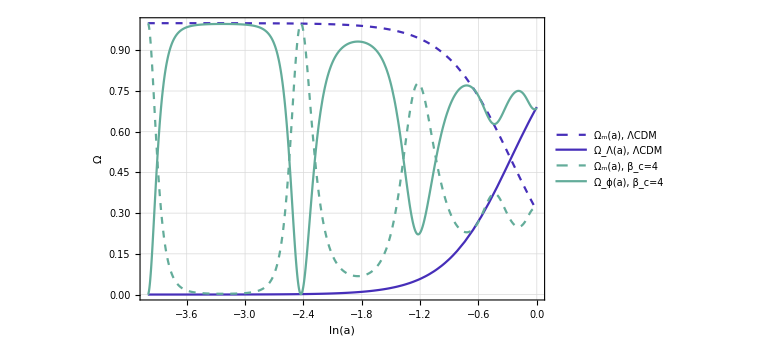

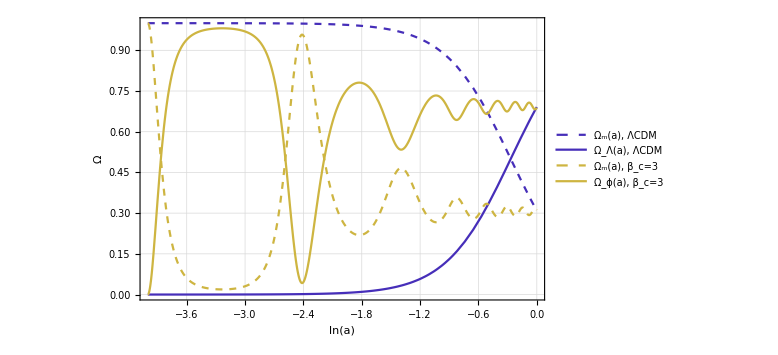

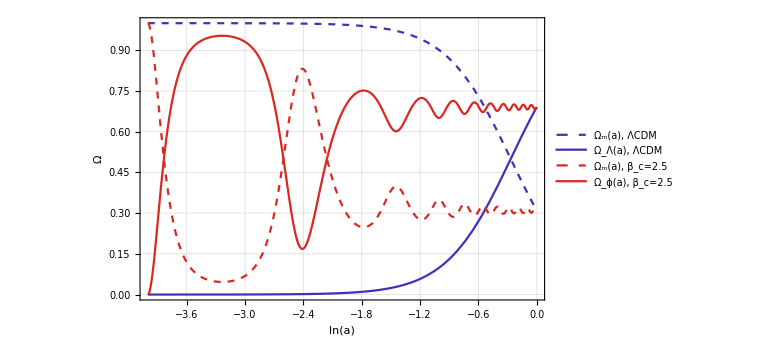

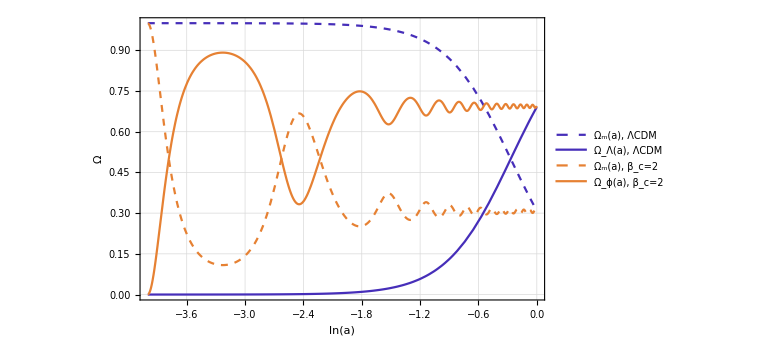

```mathematica
Ωplot2=Plot[{3*Subscript[Ω0, m]*Exp[-3n]*Exp[2n]/(3*bgtot[[1,8]]^2),  3*Subscript[Ω0, ϕ]*Exp[2n]/(3*bgtot[[1,8]]^2),
bgtot[[3,3]]/3/(Exp[-n]*bgtot[[3,8]])^2,bgtot[[3,9]]/3/(Exp[-n]*bgtot[[3,8]])^2}, {n, ni,nf},Frame->True, PlotStyle->{{col1, Dashed},{col1},{col2, Dashed},{col2}},FrameLabel->{"ln(a)","Ω"},PlotLegends->Placed[LineLegend[{"Ω_m(a), ΛCDM","Ω_Λ(a), ΛCDM", "Ω_m(a), β_c=4","Ω_ϕ(a), β_c=4"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium],{.17,.27}], GridLines->Automatic,ImageSize->Large]

Ωplot3=Plot[{3*Subscript[Ω0, m]*Exp[-3n]*Exp[2n]/(3*bgtot[[1,8]]^2),  3*Subscript[Ω0, ϕ]*Exp[2n]/(3*bgtot[[1,8]]^2),
bgtot[[4,3]]/3/(Exp[-n]*bgtot[[4,8]])^2,bgtot[[4,9]]/3/(Exp[-n]*bgtot[[4,8]])^2}, {n, ni,nf},Frame->True, PlotStyle->{{col1, Dashed},{col1},{col3, Dashed},{col3}},FrameLabel->{"ln(a)","Ω"},PlotLegends->Placed[LineLegend[{"Ω_m(a), ΛCDM","Ω_Λ(a), ΛCDM", "Ω_m(a), β_c=3","Ω_ϕ(a), β_c=3"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium],{.17,.27}], GridLines->Automatic,ImageSize->Large]

Ωplot4=Plot[{3*Subscript[Ω0, m]*Exp[-3n]*Exp[2n]/(3*bgtot[[1,8]]^2),  3*Subscript[Ω0, ϕ]*Exp[2n]/(3*bgtot[[1,8]]^2),
bgtot[[5,3]]/3/(Exp[-n]*bgtot[[5,8]])^2,bgtot[[5,9]]/3/(Exp[-n]*bgtot[[5,8]])^2}, {n, ni,nf},Frame->True, PlotStyle->{{col1, Dashed},{col1},{col4, Dashed},{col4},{col5, Dashed},{col5}},FrameLabel->{"ln(a)","Ω"},PlotLegends->Placed[LineLegend[{"Ω_m(a), ΛCDM","Ω_Λ(a), ΛCDM", "Ω_m(a), β_c=2.5","Ω_ϕ(a), β_c=2.5"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium],{.17,.27}], GridLines->Automatic,ImageSize->Large]

Ωplot5=Plot[{3*Subscript[Ω0, m]*Exp[-3n]*Exp[2n]/(3*bgtot[[1,8]]^2),  3*Subscript[Ω0, ϕ]*Exp[2n]/(3*bgtot[[1,8]]^2),
bgtot[[6,3]]/3/(Exp[-n]*bgtot[[6,8]])^2,bgtot[[6,9]]/3/(Exp[-n]*bgtot[[6,8]])^2}, {n, ni,nf},Frame->True, PlotStyle->{{col1, Dashed},{col1},{col5, Dashed},{col5}},FrameLabel->{"ln(a)","Ω"},PlotLegends->Placed[LineLegend[{"Ω_m(a), ΛCDM","Ω_Λ(a), ΛCDM","Ω_m(a), β_c=2","Ω_ϕ(a), β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium],{.17,.27}], GridLines->Automatic,ImageSize->Large]
```

## Chapter 3: Cosmological perturbations

In this chapter we deal with the computation of the solutions to the perturbation equations. We solve both the exact system of differential equations and the quasi-static-approximated system. Two loops allow us to perform all the necessary computations. Each loop contains a NDSolve fuction for the straigthforward solution of the perturbation equations for a fixed value of k. It also contains a ParametricNDSolve function for solving the same system in case of generic k. In this way, we can build a matrix (using the Table function) that shows the dependence of the matter-density constrast δ_m on the wave number k.

## EXACT solutions: Perturbation equations in ΛCDM and Conformal cases

### EXACT solutions: System of differential equations in ΛCDM

```mathematica
(* setting the scale of perturbations *)
Clear[k];
kc=20;
k=kc;

(* setting the case of interest for which the Subscript[δ, m](k) Table will be computed *)
(* remember that βc=4 corresponds to i=3, βc=3 to i=4, βc=2.5 to i=5, βc=2 to i=6 in the solution matrices *)
icase=3;

(* setting the extrema of the solution interval *)
np=-2.5;
nf=0.;

(* acquiring the background solutions of ΛCDM *)
i=1;
ρm[n_]=bgtot[[i,3]];
ℋ[n_]=bgtot[[i,8]];

(* ΛCDM perturbation eqautions *)
eqmρΛCDM= ℋ[n]*δm'[n] == -θm[n] + 3*ℋ[n]*Φ'[n];
eqmθΛCDM = ℋ[n]*θm'[n] == -ℋ[n]*θm[n] + k^2*Φ[n] ;
eqeinsteinΛCDM = k^2*Φ[n] + 3*ℋ[n]^2*(Φ'[n] + Φ[n]) == -1/2*Exp[2n]*ρm[n]*δm[n];

pertΛCDM=NDSolve[{eqmρΛCDM,eqmθΛCDM,eqeinsteinΛCDM,
δm[np]==1.,θm[np]==1.,k^2*Φ[np] ==-1./2.*ρm[np]*Exp[2np]*δm[np]},
{δm[n],θm[n],Φ[n],n},{n, np,nf}, MaxSteps->1000000, WorkingPrecision->MachinePrecision];

δsm[n_]=δm[n]/.pertΛCDM;
θsm[n_]=θm[n]/.pertΛCDM;
Φs[n_]=Φ[n]/.pertΛCDM; 

perttot[[i,1]]=δsm[n];
perttot[[i,4]]=θsm[n];
perttot[[i,5]]=Φs[n]; 

(* ΛCDM perturbation eqautions in function of k *)

Clear[k];

pertk=ParametricNDSolve[{eqmρΛCDM,eqmθΛCDM,eqeinsteinΛCDM,
δm[np]==1.,θm[np]==0.,k^2*Φ[np] ==-1./2.*ρm[np]*Exp[2np]*δm[np]},
{δm,θm,Φ},{n, np,nf},{k}, MaxSteps->100000000, WorkingPrecision->MachinePrecision];

pertkΛCDM=Table[{(δm[k][n]/.pertk)},{k,{20, 50, 100, 1000, 10000}}];
```

### EXACT solutions: System of differential equations in Conformal coupling

```mathematica
(* solving the exact system of perturbation equations for the conformal coupling cases *)
Clear[i,k];

For[i=3, i<7, i++,{
Clear[ℋ,mv, ϕ, q, c, d, v, ρm,Φ, δm, δϕ, θm, k, eqmρ,eqmθ,eqeinstein2,eqeinstein,eqϕ, Μ2, ℳ2, ℬ1, ℬ5];

k=kc;

(* acquiring the background solutions *)
ϕ[n_]=bgtot[[i,1]];
ρm[n_]=bgtot[[i,3]];
mvn[n_]=bgtot[[i,4]];
mv=mvn[0];

(* setting the choices of parameters *)
Which[ 
i==2, {c0=1.; βc=0.; c[n_]:=1.; dc[n_]:=0; ddc[n_]:=0; d[n_]:=0.; q[n_]:=0.,v0=3*Subscript[Ω0, ϕ]},
i==3,{c0=1.; βc=βcb1; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==4,{c0=1.; βc=βcb2; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==5,{c0=1.; βc=βcb3; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==6,{c0=1.; βc=βcb4; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0}
 ];

(* redefining some useful functions with the acquired solutions *)
v[n_]:=1/2 mv^2*ϕ[n]^2 +v0;
dv[n_]:=1/2mv^2*ϕ[n]*2;
ddv[n_]:=1/2mv^2*2;
ℋ[n_]=bgtot[[i,8]];
ξ[n_]:=ℋ'[n]/ℋ[n];
ρϕ[n_]:=(1./2.)*(ℋ[n]*Exp[-n])^2*ϕ'[n]^2 + v[n];

(* numerator and denominator of the coupling function Q *)
Α[n_]:=Exp[2n]*c[n];
Β[n_]:=Exp[2n]*dc[n];

(* perturbed coupling function *)
δq[n_]:=-1./Α[n]*(ℬ1[n]*(δm[n]) +ℬ5[n]*δϕ[n]) ;
ℬ1[n_]:=Β[n]/2 ;
ℬ5[n_]:=Exp[2n]*ddc[n]/2  +  (Exp[2n]*dc[n])*q[n];

(* perturbation equations *)
eqmρ= δm'[n]*ℋ[n]== -θm[n] + 3*Φ'[n]*ℋ[n] + (q[n])*ϕ'[n]*δm[n]*ℋ[n] - ϕ'[n]*δq[n]*ℋ[n] - (q[n])*δϕ'[n]*ℋ[n];
eqmθ= θm'[n]*ℋ[n]== -θm[n]*ℋ[n] + k^2*Φ[n] + (q[n])*ϕ'[n]*θm[n] *ℋ[n]- (q[n])*k^2*δϕ[n];
eqeinstein= k^2*Φ[n] + 3*(Φ'[n] + Φ[n])*(ℋ[n]^2)==-1/2*ρm[n]*Exp[2n]*δm[n]- 1/2*(ℋ[n]^2)*(ϕ'[n]*δϕ'[n] - Φ[n]*(ϕ'[n])^2 + Exp[2n]*dv[n]*δϕ[n]/(ℋ[n]^2));
eqeinstein2= Φ''[n] +( 3+ξ[n])Φ'[n] + (1 + 2*ξ[n])Φ[n]==1/2*(ϕ'[n]*δϕ'[n] - Φ[n]*(ϕ'[n])^2 - Exp[2n]*dv[n]*δϕ[n]/(ℋ[n]^2));
eqϕ= δϕ''[n]*(ℋ[n]^2) +(2+ξ[n])*δϕ'[n] *(ℋ[n]^2)+ (k^2 + Exp[2n]*ddv[n])*δϕ[n]==
4*ϕ'[n]*Φ'[n]*(ℋ[n]^2)  - 2*Exp[2n]*(dv[n]-q[n]*ρm[n])*Φ[n] + Exp[2n]*δq[n]*ρm[n];
eqΦΨ= Φ[n]==Ψ[n];

(* numerical solutions to perturbation equations *) 
pertconf=NDSolve[{eqmρ,eqmθ,eqeinstein,eqϕ,
δm[np]==1.,δϕ[np]==1.,δϕ'[np]==1.,θm[np]==1.,k^2*Φ[np] ==-3./2.*ρm[np]*Exp[2np]/(3.)*δm[np]},
{δm[n],δϕ[n],δϕ'[n],θm[n],Φ[n],n},{n, np,nf}, MaxSteps->1000000, WorkingPrecision->MachinePrecision];

(* extracting the solutions *)
δsm[n_]=δm[n]/.pertconf[[1]];
δsϕ[n_]=δϕ[n]/.pertconf;
dδsϕ[n_]=δϕ'[n]/.pertconf;
θsm[n_]=θm[n]/.pertconf;
Φs[n_]=Φ[n]/.pertconf; 

(* insertin the solutions into the matrix *)
perttot[[i,1]]=δsm[n];
perttot[[i,2]]=δsϕ[n];
perttot[[i,3]]=dδsϕ[n];
perttot[[i,4]]=θsm[n];
perttot[[i,5]]=Φs[n];

(* comparison between different perturbation growths for different k *)
(* only the case i=icase is computed *)

If[i==icase, {
Clear[ℋ,mv, ϕ, q, c, d, v,Φ, ρm, δm, δϕ, θm, k,eqmρ,eqmθ,eqeinstein,eqeinstein2,eqϕ, Μ2, ℳ2, ℬ1, ℬ5];

(* acquiring the background solutions *)
ϕ[n_]=bgtot[[i,1]];
ρm[n_]=bgtot[[i,3]];
mvn[n_]=bgtot[[i,4]];
mv=mvn[0];

(* setting the choices of parameters *)
Which[ 
i==2, {c0=1.; βc=0.; c[n_]:=1.; dc[n_]:=0; ddc[n_]:=0; d[n_]:=0.; q[n_]:=0.,v0=3*Subscript[Ω0, ϕ]},
i==3,{c0=1.; βc=βcb1; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==4,{c0=1.; βc=βcb2; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==5,{c0=1.; βc=βcb3; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==6,{c0=1.; βc=βcb4; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0}
 ];

v[n_]:=1/2mv^2*ϕ[n]^2 +v0;
dv[n_]:=1/2mv^2*ϕ[n]*2;
ddv[n_]:=1/2mv^2*2;
ℋ[n_]=bgtot[[i,8]];
ξ[n_]:=ℋ'[n]/ℋ[n];

(* numerator and denominator of the coupling function Q *) 
Α[n_]:=Exp[2n]*c[n];
Β[n_]:=Exp[2n]*dc[n];

(* perturbed coupling function *)
δq[n_]:=-1./Α[n]*(ℬ1[n]*(δm[n]) +ℬ5[n]*δϕ[n]) ;
ℬ1[n_]:=Β[n]/2 ;
ℬ5[n_]:=Exp[2n]*ddc[n]/2  +  (Exp[2n]*dc[n])*q[n];

(* perturbation equations *)
eqmρ= δm'[n]*ℋ[n]== -θm[n] + 3*Φ'[n]*ℋ[n] + (q[n])*ϕ'[n]*δm[n]*ℋ[n] - ϕ'[n]*δq[n]*ℋ[n] - (q[n])*δϕ'[n]*ℋ[n];
eqmθ= θm'[n]*ℋ[n]== -θm[n]*ℋ[n] + k^2*Φ[n] + (q[n])*ϕ'[n]*θm[n] *ℋ[n]- (q[n])*k^2*δϕ[n];
eqeinstein= k^2*Φ[n] + 3*(Φ'[n] + Φ[n])*(ℋ[n]^2)==-1/2*ρm[n]*Exp[2n]*δm[n]- 1/2*(ℋ[n]^2)*(ϕ'[n]*δϕ'[n] - Φ[n]*(ϕ'[n])^2 + Exp[2n]*dv[n]*δϕ[n]/(ℋ[n]^2));
eqeinstein2= Φ''[n] +( 3+ξ[n])Φ'[n] + (1 + 2*ξ[n])Φ[n]==1/2*(ϕ'[n]*δϕ'[n] - Φ[n]*(ϕ'[n])^2 - Exp[2n]*dv[n]*δϕ[n]/(ℋ[n]^2));
eqϕ= δϕ''[n]*(ℋ[n]^2) +(2+ξ[n])*δϕ'[n] *(ℋ[n]^2)+ (k^2 + Exp[2n]*ddv[n])*δϕ[n]==
4*ϕ'[n]*Φ'[n]*(ℋ[n]^2)  - 2*Exp[2n]*(dv[n]-q[n]*ρm[n])*Φ[n] + Exp[2n]*δq[n]*ρm[n];
eqΦΨ= Φ[n]==Ψ[n];

pertk=ParametricNDSolve[{eqmρ,eqmθ,eqeinstein,eqϕ,
δm[np]==1.,δϕ[np]==1.,δϕ'[np]==1.,θm[np]==1.,k^2*Φ[np] ==-3./2.*ρm[np]*Exp[2np]/(3.)*δm[np]},
{δm,δϕ,δϕ',θm},{n, np,nf},{k}, MaxSteps->100000000, WorkingPrecision->MachinePrecision];

pertkconf=Table[{(δm[k][n]/.pertk)},{k,{20, 50, 100, 1000, 10000}}]}];
}]
```

## QUASI-STATIC solutions: Perturbation equations in Conformal coupling

### QUASI-STATIC solutions: System of differential equations

```mathematica
Clear[i,k];

For[i=3, i<7, i++,{
Clear[ℋ,mv, ϕ, q, c, d, v, ρ,Φ, y, α2, α0, β2, β0, Μ2, ℳ2,  ρm, δm, δϕ, θm, k, eqδm, eqδm1, eqδm2, Μ2, ℳ2];

k=kc;

ϕ[n_]=bgtot[[i,1]];
ρm[n_]=bgtot[[i,3]];
mvn[n_]=bgtot[[i,4]];
mv=mvn[0];

Which[ 
i==2, {c0=1.; βc=0.; c[n_]:=1.; dc[n_]:=0; ddc[n_]:=0; d[n_]:=0.; q[n_]:=0.,v0=3*Subscript[Ω0, ϕ]},
i==3,{c0=1.; βc=βcb1; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==4,{c0=1.; βc=βcb2; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==5,{c0=1.; βc=βcb3; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==6,{c0=1.; βc=βcb4; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0}
 ];

v[n_]:=1/2mv^2*ϕ[n]^2 +v0;
dv[n_]:=1/2mv^2*ϕ[n]*2;
ddv[n_]:=1/2mv^2*2;
ℋ[n_]=bgtot[[i,8]];
ξ[n_]:=ℋ'[n]/ℋ[n];

(* numerator and denominator of the coupling function Q *) 
Α[n_]:=Exp[2n]*c[n];
Β[n_]:=Exp[2n]*dc[n];

(* perturbation equations *)
Μ2[n_]:=Exp[2n]*ddv[n];
dΜ2[n_]:=Μ2'[n];
ℳ2[n_]:=ρm[n]*βc*Exp[2n];
dℳ2[n_]:=ℳ2'[n];
f[n_]:=1+ξ[n] - (-βc*ϕ[n])*ϕ'[n] - (-βc*ϕ[n])*ϕ'[n]*(ℳ2[n])/(k^2 + Μ2[n]+ ℳ2[n]);
g[n_]:= ((1+ξ[n]-(-βc*ϕ[n])*ϕ'[n])*(-βc*ϕ[n])*ϕ'[n] + (((-βc*ϕ'[n])*ϕ'[n])+(-βc*ϕ[n])*ϕ''[n]))/(Exp[2n]*ρm[n]/(ℋ[n]^2)*(-βc*ϕ[n])^2);
α2[n_]:=ϕ'[n]/(ρm[n]*Exp[2n]/(ℋ[n]^2)*(-βc*ϕ[n]))*(dℳ2[n]) + (Μ2[n] + ℳ2[n]) + g[n]*ℳ2[n];
α0[n_]:=ϕ'[n]/(ρm[n]*Exp[2n]/(ℋ[n]^2)*(-βc*ϕ[n]))*(dℳ2[n]*Μ2[n] - dΜ2[n]*ℳ2[n]) + ℳ2[n]*(ℳ2[n] + Μ2[n])*g[n];
β2[n_]:=2*(ℳ2[n]+ Μ2[n]);
β0[n_]:=(ℳ2[n]+ Μ2[n])^2;
y[n_]:=2*(-βc*ϕ[n])^2*(k^4 + α2[n]*k^2 + α0[n])/(k^4 + β2[n]*k^2 + β0[n]);

eqδm1 = δm'[n]* ℋ[n]== -θm[n] + ℳ2[n]*q[n]*ϕ'[n]*δm[n]*ℋ[n]/(k^2 + Μ2[n] + ℳ2[n]);
eqδm2 = θm'[n]==-θm[n] - 1/2*ρm[n]*Exp[2n]/(ℋ[n])*δm[n] + q[n]*ϕ'[n]*θm[n] - q[n]^2*ρm[n]*Exp[2n]/(ℋ[n])*k^2*δm[n]/(k^2 + Μ2[n] + ℳ2[n]);

(* numerical solutions to perturbation equations *) 
pertapprox=NDSolve[{eqδm1,eqδm2,δm[np]==1, θm[np]==1 },
{δm[n],θm[n],n},{n, np,nf}, MaxSteps->1000000, WorkingPrecision->MachinePrecision];

δsam[n_]=δm[n]/.pertapprox[[1]];

perttot[[i, 6]]=δsam[n];
perttot[[i, 7]]=y[n];(* Y function in the QSA *)
perttot[[i, 8]]=(-2(q'[n])^2)/(k^2 + ℳ2[n] +Μ2[n]); (* Y function in the weak-gravity regime *)
perttot[[i, 9]]=δsamf[n];
perttot[[i,10]]=δsamy[n];
perttot[[i,11]]=f[n];

(* comparison between different perturbation growths for different k *)
(* only the case i=icase is computed *)

If[i==icase,{
Clear[ℋ,mv, ϕ, q, c, d, v, ρ, y, α2, α0, β2, β0, Μ2, ℳ2,  ρm, δm, δϕ, θm, k, eqδm, eqδm1, eqδm2, Μ2, ℳ2];

ϕ[n_]=bgtot[[i,1]];
ρm[n_]=bgtot[[i,3]];
mvn[n_]=bgtot[[i,4]];
mv=mvn[0];

Which[ 
i==2, {c0=1.; βc=0.; c[n_]:=1.; dc[n_]:=0; ddc[n_]:=0; d[n_]:=0.; q[n_]:=0.,v0=3*Subscript[Ω0, ϕ]},
i==3,{c0=1.; βc=βcb1; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==4,{c0=1.; βc=βcb2; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==5,{c0=1.; βc=βcb3; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0},
i==6,{c0=1.; βc=βcb4; c[n_]:=c0*Exp[βc*ϕ[n]^2]; dc[n_]:=βc*2*ϕ[n]*c[n]; ddc[n_]:=βc*2*ϕ[n]*dc[n] + βc*2*c[n]; d[n_]:=0.; q[n_]:=-βc*ϕ[n]; v0=0}
 ];

v[n_]:=1/2mv^2*ϕ[n]^2 +v0;
dv[n_]:=1/2mv^2*ϕ[n]*2;
ddv[n_]:=1/2mv^2*2;
ℋ[n_]=bgtot[[i,8]];
ξ[n_]:=ℋ'[n]/ℋ[n];

(* numerator and denominator of the coupling function Q *) 
Α[n_]:=Exp[2n]*c[n];
Β[n_]:=Exp[2n]*dc[n];

ρϕ[n_]:=(1./2.)*(ℋ[n]*Exp[-n])^2*ϕ'[n]^2 + v[n];

(* perturbation equations *)
Μ2[n_]:=Exp[2n]*ddv[n];
dΜ2[n_]:=Μ2'[n];
ℳ2[n_]:=ρm[n]*βc*Exp[2n];
dℳ2[n_]:=ℳ2'[n];

eqδm1 = δm'[n]* ℋ[n]== -θm[n] + ℳ2[n]*q[n]*ϕ'[n]*δm[n]*ℋ[n]/(k^2 + Μ2[n] + ℳ2[n]);
eqδm2 = θm'[n]==-θm[n] - 1/2*ρm[n]*Exp[2n]/(ℋ[n])*δm[n] + q[n]*ϕ'[n]*θm[n] - q[n]^2*ρm[n]*Exp[2n]/(ℋ[n])*k^2*δm[n]/(k^2 + Μ2[n] + ℳ2[n]);

pertkapprox=ParametricNDSolve[{eqδm1, eqδm2,δm[np]==1, θm[np]==1},
{δm, θm},{n, np,nf},{k}, MaxSteps->100000000, WorkingPrecision->MachinePrecision];

pertkconfapp=Evaluate[Table[{((δm[k][n])/.pertkapprox)},{k,{20, 50, 100, 1000, 10000}}]]}];

}]
```

## Perturbation plots

In this final set of plots, we aim at detecting the onset of the weak-gravity regime by comparing the values of the Y function in the quasi-static approximation and in the weak-gravity regime. When the two coincide, the Y function acts as a negative correction to the Newtonian potential thus producing a weakening of the gravitational interaction.

Firstly, we will plot some generic comparison among the matter density-contrasts of the four conformally-coupled scenarios. Secondly, we will investigate the matching between the exact solutions and the QSA solutions: in this way, we can infer the interval in which the QSA is a good approximation of the exact system. Lastly, we will compare the Y functions in the QSA and weak-gravity regimes. The onset of the weak-gravity regime has also noticeable effects on the growth of perturbation as the last figure will show.

Since the background cosmology has highlighted strong differences between the coupled cases and the uncoupled/ΛCDM cases, we will focus only on the four versions of the conformal-coupling model in the following.

### δ_m(a) plots

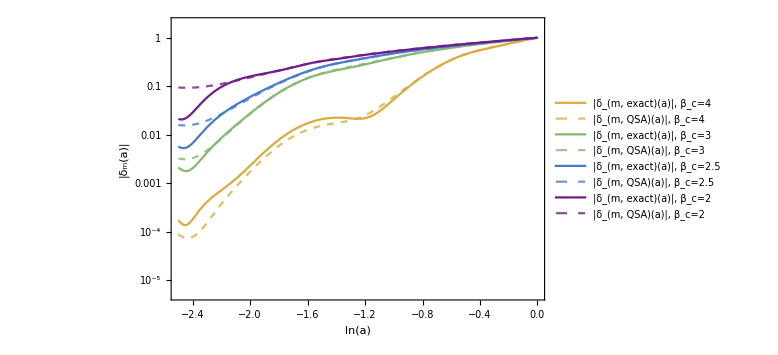

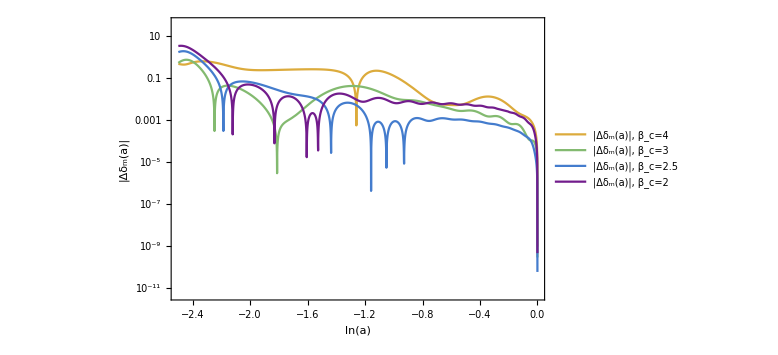

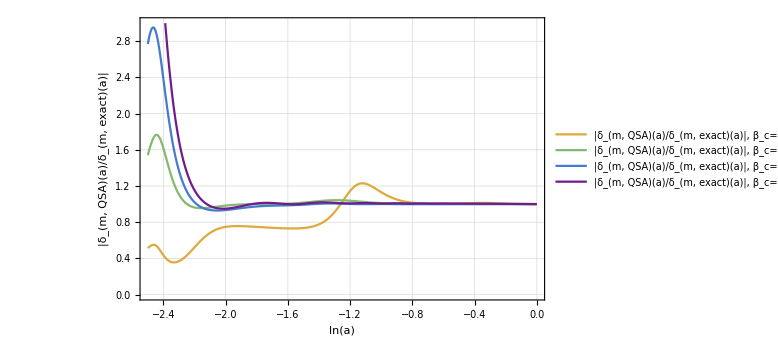

```mathematica
(* colours used in the article *)
col=ColorData["Rainbow"];
col1=col[.99];
col2=col[.75];
col3=col[.50];
col4=col[.25];
col5=col[.01];
col6=col[.12];
col7=col[.32];
col8=col[.62];
col9=col[.82];

(* extracting the solutions from the matrix perttot *)
Subscript[δsunc, m][n_]=perttot[[2,1]];
Subscript[δ4, m][n_]=perttot[[3,1]];
Subscript[δ3, m][n_]=perttot[[4,1]];
Subscript[δ25, m][n_]=perttot[[5,1]];
Subscript[δ2, m][n_]=perttot[[6,1]];
Subscript[δ4a, m][n_]=perttot[[3,6]];
Subscript[δ3a, m][n_]=perttot[[4,6]];
Subscript[δ25a, m][n_]=perttot[[5,6]];
Subscript[δ2a, m][n_]=perttot[[6,6]];

(* Plotting the evolution of Subscript[δ, m](a). All the perturbations are normalised to their present value *)
δsmplot1=LogPlot[{ perttot[[3,1]]/Subscript[δ4, m][nf], perttot[[3,6]]/Subscript[δ4a, m][nf], perttot[[4,1]]/Subscript[δ3, m][nf], perttot[[4,6]]/Subscript[δ3a, m][nf],  perttot[[5,1]]/Subscript[δ25, m][nf], perttot[[5,6]]/Subscript[δ25a, m][nf],  perttot[[6,1]]/Subscript[δ2, m][nf], perttot[[6,6]]/Subscript[δ2a, m][nf]},{n, np, nf}, Frame->True,PlotStyle->{{col2},{col2, Dashed, Opacity[0.8]}, {col3},{col3, Dashed, Opacity[0.8]}, {col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","|δ_m(a)|"},PlotRange->{5*10^(-6),2},PlotLegends->Placed[LineLegend[{"|δ_(m, exact)(a)|, β_c=4", "|δ_(m,  QSA)(a)|, β_c=4","|δ_(m, exact)(a)|, β_c=3", "|δ_(m,  QSA)(a)|, β_c=3","|δ_(m, exact)(a)|, β_c=2.5", "|δ_(m,  QSA)(a)|, β_c=2.5", "|δ_(m, exact)(a)|, β_c=2", "|δ_(m,  QSA)(a)|, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger], {.8, .38}], GridLines->Automatic,ImageSize->Large, PlotPoints->50]

Δδsmplot1=LogPlot[{  
Abs[(perttot[[3,1]]/Subscript[δ4, m][nf]-perttot[[3,6]]/Subscript[δ4a, m][nf])/(perttot[[3,1]]/Subscript[δ4, m][nf])],
Abs[(perttot[[4,1]]/Subscript[δ3, m][nf]-perttot[[4,6]]/Subscript[δ3a, m][nf])/(perttot[[4,1]]/Subscript[δ3, m][nf])], 
Abs[(perttot[[5,1]]/Subscript[δ25, m][nf]-perttot[[5,6]]/Subscript[δ25a, m][nf])/(perttot[[5,1]]/Subscript[δ25, m][nf])],
Abs[(perttot[[6,1]]/Subscript[δ2, m][nf]-perttot[[6,6]]/Subscript[δ2a, m][nf])/(perttot[[6,1]]/Subscript[δ2, m][nf])]},{n, np, nf}, Frame->True,PlotStyle->{{col2}, {col3},{col4},{col5}},FrameLabel->{"ln(a)","|Δδ_m(a)|"},PlotRange->All,PlotLegends->Placed[LineLegend[{"|Δδ_m(a)|, β_c=4", "|Δδ_m(a)|, β_c=3", "|Δδ_m(a)|, β_c=2.5", "|Δδ_m(a)|, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger], {.78, .3}], GridLines->Automatic,ImageSize->Large, PlotPoints->50]

δsmplotrel1=Plot[{ 
Abs[(perttot[[3,6]]/Subscript[δ4a, m][nf])/(perttot[[3,1]]/Subscript[δ4, m][nf])],
Abs[(perttot[[4,6]]/Subscript[δ3a, m][nf])/(perttot[[4,1]]/Subscript[δ3, m][nf])], 
Abs[(perttot[[5,6]]/Subscript[δ25a, m][nf])/(perttot[[5,1]]/Subscript[δ25, m][nf])],
Abs[(perttot[[6,6]]/Subscript[δ2a, m][nf])/(perttot[[6,1]]/Subscript[δ2, m][nf])]},{n, np, nf}, Frame->True,PlotStyle->{{col2}, {col3},{col4},{col5}},FrameLabel->{"ln(a)","|δ_(m, QSA)(a)/δ_(m, exact)(a)|"},PlotRange->{0, 3},PlotLegends->Placed[LineLegend[{"|δ_(m, QSA)(a)/δ_(m, exact)(a)|, β_c=4", "|δ_(m, QSA)(a)/δ_(m, exact)(a)|, β_c=3", "|δ_(m, QSA)(a)/δ_(m, exact)(a)|, β_c=2.5",  "|δ_(m, QSA)(a)/δ_(m, exact)(a)|, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger], {.75, .77}], GridLines->Automatic,ImageSize->Large, PlotPoints->50]
```

### δ_m(k) plots

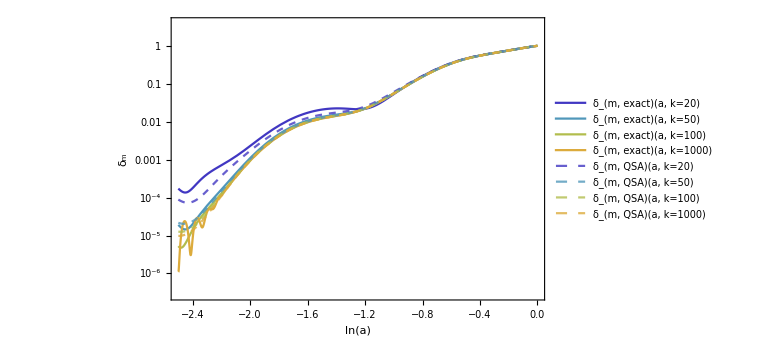

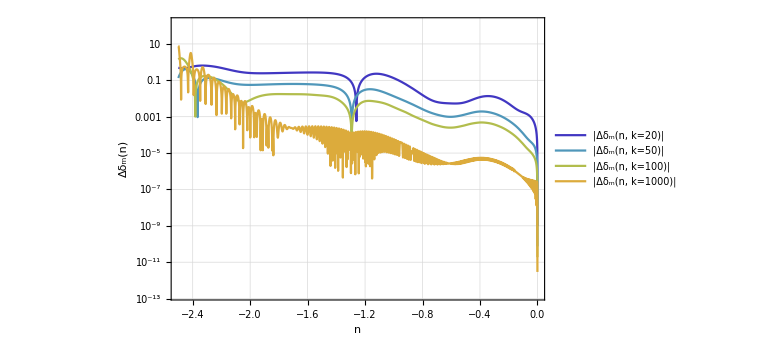

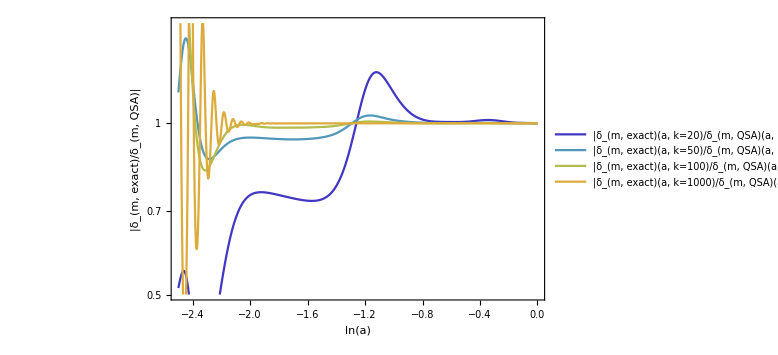

```mathematica
(* extracting the solution from the pertkconf and pertkconfapp lists *)
δk1[n_]=pertkconf[[1]];
δk2[n_]=pertkconf[[2]];
δk3[n_]=pertkconf[[3]];
δk4[n_]=pertkconf[[4]];
δk5[n_]=pertkconf[[5]];

δka1[n_]=pertkconfapp[[1]];
δka2[n_]=pertkconfapp[[2]];
δka3[n_]=pertkconfapp[[3]];
δka4[n_]=pertkconfapp[[4]];
δka5[n_]=pertkconfapp[[5]];

(* Plotting the evolution of Subscript[δ, m](a,k) *)
δsmkplot=LogPlot[{pertkconf[[1]]/δk1[nf],pertkconf[[2]]/δk2[nf],pertkconf[[3]]/δk3[nf],pertkconf[[4]]/δk4[nf],pertkconfapp[[1]]/δka1[nf], pertkconfapp[[2]]/δka2[nf], pertkconfapp[[3]]/δka3[nf], pertkconfapp[[4]]/δka4[nf]}, {n, np, nf}, Frame->True,FrameLabel->{"ln(a)","δ_m"},PlotStyle->{{col6},{col7},{col8},{col2},{col6, Dashed, Opacity[0.8]}, {col7, Dashed, Opacity[0.8]}, {col8, Dashed, Opacity[0.8]},{col2, Dashed, Opacity[0.8]}},  PlotLegends->Placed[LineLegend[{ "δ_(m, exact)(a, k=20)", "δ_(m, exact)(a, k=50)", "δ_(m, exact)(a, k=100)", "δ_(m, exact)(a, k=1000)", "δ_(m, QSA)(a, k=20)", "δ_(m, QSA)(a, k=50)", "δ_(m, QSA)(a, k=100)",  "δ_(m, QSA)(a, k=1000)"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.60, .27}], GridLines->Automatic, ImageSize->Large]

Δδsmkplot=LogPlot[{Abs[(pertkconf[[1]]/δk1[nf]-pertkconfapp[[1]]/δka1[nf])/(pertkconf[[1]]/δk1[nf])],
Abs[(pertkconf[[2]]/δk2[nf]-pertkconfapp[[2]]/δka2[nf])/(pertkconf[[2]]/δk2[nf])],
Abs[(pertkconf[[3]]/δk3[nf]-pertkconfapp[[3]]/δka3[nf])/(pertkconf[[3]]/δk3[nf])],
Abs[(pertkconf[[4]]/δk4[nf]-pertkconfapp[[4]]/δka4[nf])/(pertkconf[[4]]/δk4[nf])]}, {n, np, nf}, Frame->True,FrameLabel->{"n","Δδ_m(n)"},PlotStyle->{{col6},{col7},{col8},{col2}},  PlotLegends->Placed[LineLegend[{ "|Δδ_m(n, k=20)|", "|Δδ_m(n, k=50)|", "|Δδ_m(n, k=100)|", "|Δδ_m(n, k=1000)|"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],After], GridLines->Automatic, ImageSize->Large]

δsmkplotrel=LogPlot[{Abs[(pertkconfapp[[1]]/δka1[nf])/(pertkconf[[1]]/δk1[nf])],
Abs[(pertkconfapp[[2]]/δka2[nf])/(pertkconf[[2]]/δk2[nf])],
Abs[(pertkconfapp[[3]]/δka3[nf])/(pertkconf[[3]]/δk3[nf])],
Abs[(pertkconfapp[[4]]/δka4[nf])/(pertkconf[[4]]/δk4[nf])]}, {n, np, nf}, Frame->True,FrameLabel->{"ln(a)","|δ_(m, exact)/δ_(m, QSA)|"},PlotStyle->{{col6},{col7},{col8},{col2}},  PlotLegends->Placed[LineLegend[{ "|δ_(m, exact)(a, k=20)/δ_(m, QSA)(a, k=20)|", "|δ_(m, exact)(a, k=50)/δ_(m, QSA)(a, k=50)|", "|δ_(m, exact)(a, k=100)/δ_(m, QSA)(a, k=100)|", "|δ_(m, exact)(a, k=1000)/δ_(m, QSA)(a, k=1000)|"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Larger],{.71, .22}], GridLines->Automatic, ImageSize->Large, PlotRange->{0.5,1.5}]
```

### Y plots

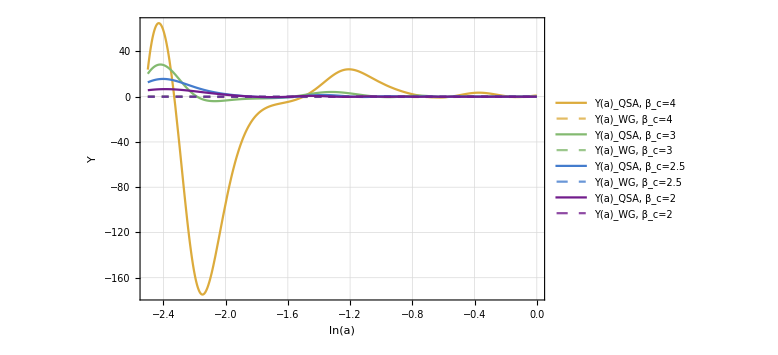

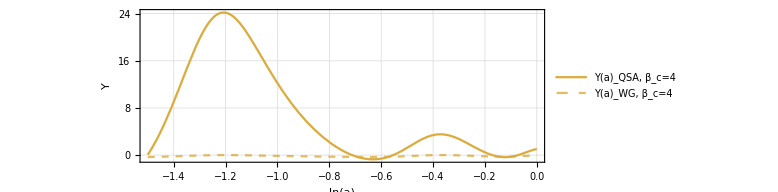

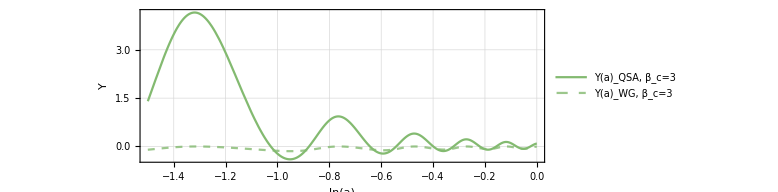

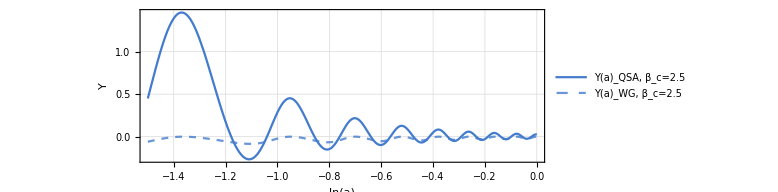

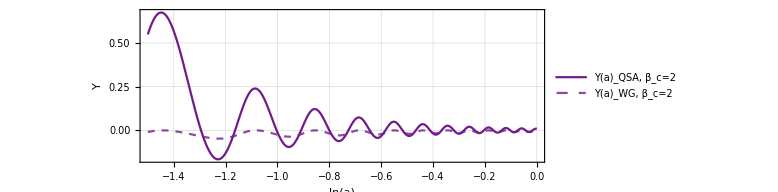

```mathematica
(* Plotting the Y functions for the four versions of the conformal-coupling model *)

Yplottot1=Plot[{perttot[[3,7]], perttot[[3,8]], perttot[[4,7]], perttot[[4,8]], perttot[[5, 7]], perttot[[5,8]], perttot[[6, 7]], perttot[[6,8]]},{n, np, nf}, Frame->True,PlotStyle->{{col2},{col2, Dashed, Opacity[0.8]}, {col3},{col3, Dashed, Opacity[0.8]}, {col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y"},PlotRange->All,PlotLegends->Placed[LineLegend[{"Y(a)_QSA, β_c=4", "Y(a)_WG, β_c=4","Y(a)_QSA, β_c=3", "Y(a)_WG, β_c=3", "Y(a)_QSA, β_c=2.5", "Y(a)_WG, β_c=2.5", "Y(a)_QSA, β_c=2", "Y(a)_WG, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.82, .3}], GridLines->Automatic,ImageSize->Large, PlotPoints->50]

Yplottot2=Plot[{perttot[[3,7]], perttot[[3,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{ {col2},{col2, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y"},PlotRange->All,PlotLegends->Placed[LineLegend[{ "Y(a)_QSA, β_c=4", "Y(a)_WG, β_c=4"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.7,.8}], GridLines->Automatic,ImageSize->Large, PlotPoints->50, AspectRatio->1/3]

Yplottot3=Plot[{perttot[[4,7]], perttot[[4,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{ {col3},{col3, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y"},PlotRange->All,PlotLegends->Placed[LineLegend[{"Y(a)_QSA, β_c=3", "Y(a)_WG, β_c=3"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.7,.8}], GridLines->Automatic,ImageSize->Large, PlotPoints->50, AspectRatio->1/3]

Yplottot4=Plot[{perttot[[5,7]], perttot[[5,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col4},{col4, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y"},PlotRange->All,PlotLegends->Placed[LineLegend[{"Y(a)_QSA, β_c=2.5", "Y(a)_WG, β_c=2.5"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.7,.8}], GridLines->Automatic,ImageSize->Large, PlotPoints->50, AspectRatio->1/3]

Yplottot5=Plot[{perttot[[6,7]], perttot[[6,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y"},PlotRange->All,PlotLegends->Placed[LineLegend[{"Y(a)_QSA, β_c=2", "Y(a)_WG, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.7,.8}], GridLines->Automatic,ImageSize->Large, PlotPoints->50, AspectRatio->1/3]
```

### Weak gravity plots

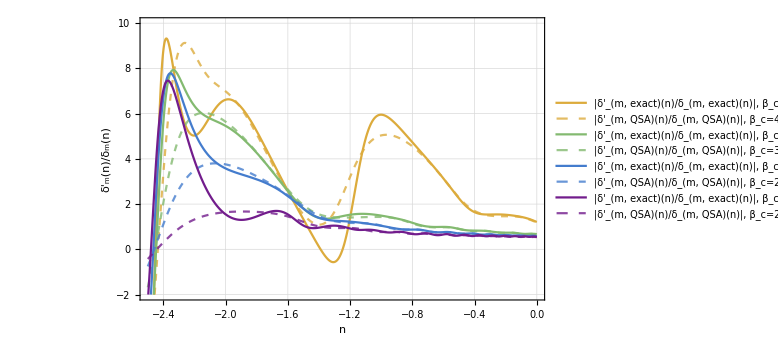

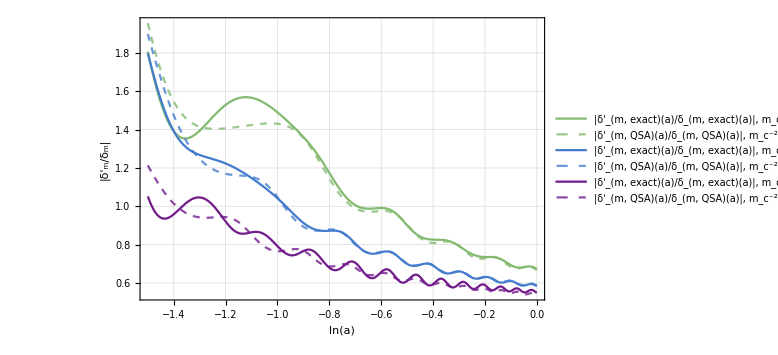

```mathematica
(* Plotting the ratio Subscript[δ', m](a)/Subscript[δ, m](a) for the four versions of conformal-coupling model *)

δsmplot3=Plot[{Subscript[δ4, m]'[n]/Subscript[δ4, m][n],Subscript[δ4a, m]'[n]/Subscript[δ4a, m][n],Subscript[δ3, m]'[n]/Subscript[δ3, m][n], Subscript[δ3a, m]'[n]/Subscript[δ3a, m][n], Subscript[δ25, m]'[n]/Subscript[δ25, m][n], Subscript[δ25a, m]'[n]/Subscript[δ25a, m][n], Subscript[δ2, m]'[n]/Subscript[δ2, m][n], Subscript[δ2a, m]'[n]/Subscript[δ2a, m][n]},{n, -2.5, nf}, Frame->True,PlotStyle->{{col2},{col2, Dashed, Opacity[0.8]},{col3},{col3, Dashed, Opacity[0.8]}, {col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"n","δ'_m(n)/δ_m(n)"},PlotRange->{-2, 10},PlotLegends->Placed[LineLegend[{"|δ'_(m, exact)(n)/δ_(m, exact)(n)|, β_c=4", "|δ'_(m,  QSA)(n)/δ_(m, QSA)(n)|, β_c=4","|δ'_(m, exact)(n)/δ_(m, exact)(n)|, β_c=3", "|δ'_(m,  QSA)(n)/δ_(m, QSA)(n)|, β_c=3","|δ'_(m, exact)(n)/δ_(m, exact)(n)|, β_c=2.5", "|δ'_(m,  QSA)(n)/δ_(m, QSA)(n)|, β_c=2.5", "|δ'_(m, exact)(n)/δ_(m, exact)(n)|, β_c=2", "|δ'_(m,  QSA)(n)/δ_(m, QSA)(n)|, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], After],GridLines->Automatic, ImageSize->Large, PlotPoints->50]

δsmplot4=Plot[{ Subscript[δ3, m]'[n]/Subscript[δ3, m][n], Subscript[δ3a, m]'[n]/Subscript[δ3a, m][n], Subscript[δ25, m]'[n]/Subscript[δ25, m][n], Subscript[δ25a, m]'[n]/Subscript[δ25a, m][n], Subscript[δ2, m]'[n]/Subscript[δ2, m][n], Subscript[δ2a, m]'[n]/Subscript[δ2a, m][n]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col3},{col3, Dashed, Opacity[0.8]}, {col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","|δ'_m/δ_m|"},PlotRange->All,PlotLegends->Placed[LineLegend[{"|δ'_(m, exact)(a)/δ_(m, exact)(a)|, m_c^-2=3", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|, m_c^-2=3","|δ'_(m, exact)(a)/δ_(m, exact)(a)|, m_c^-2=2.5", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|, m_c^-2=2.5", "|δ'_(m, exact)(a)/δ_(m, exact)(a)|, m_c^-2=2", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|, m_c^-2=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium], {.75, .68}],GridLines->Automatic, ImageSize->Large, PlotPoints->50]
```

### Final plots

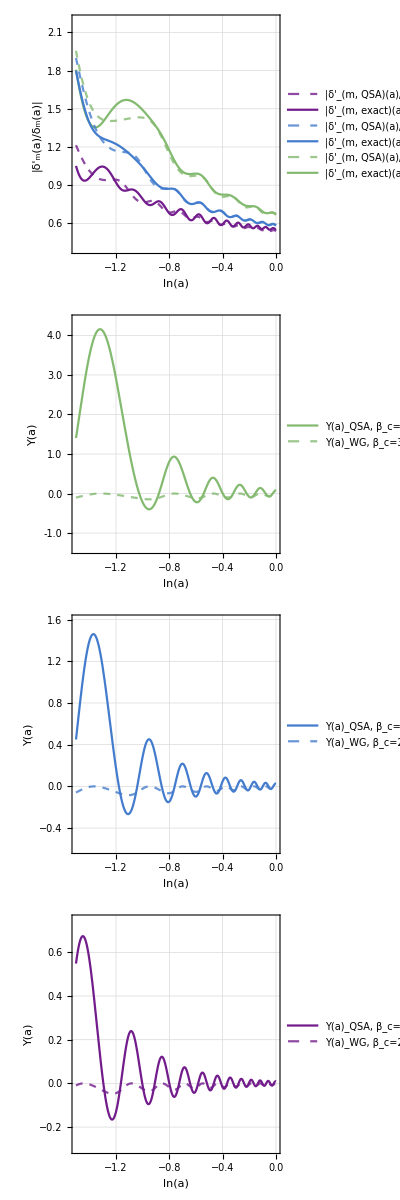

```mathematica
(* Plotting the ratio Subscript[δ', m](a)/Subscript[δ, m](a) and the Y function in the same image *)

δsmplotfin1=LogPlot[{Subscript[δ3, m][n]/Subscript[δ3, m][nf], Subscript[δ3a, m][n]/Subscript[δ3a, m][nf],  Subscript[δ25, m][n]/Subscript[δ25, m][nf], Subscript[δ25a, m][n]/Subscript[δ25a, m][nf], Subscript[δ2, m][n]/Subscript[δ2, m][nf], Subscript[δ2a, m][n]/Subscript[δ2a, m][nf]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col3},{col3, Dashed, Opacity[0.8]},{col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","|δ_m(a)|"},PlotRange->All,PlotLegends->Placed[LineLegend[{"|δ_(m, exact)(a)|,  m_c^-2=3", "|δ_(m,  QSA)(a)|,  m_c^-2=3","|δ_(m, exact)(a)|,  m_c^-2=2.5", "|δ_(m,  QSA)(a)|,  m_c^-2=2.5", "|δ_(m, exact)(a)|,  m_c^-2=2", "|δ_(m,  QSA)(a)|,  m_c^-2=2"},LegendLayout->"ReversedColumn",LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LabelStyle->Medium],{.79, .3}],ImageSize->Large, PlotPoints->50, ImagePadding->{{50, 10}, {1, 10}}];

δsmplotfin2=Plot[{ Subscript[δ3, m]'[n]/Subscript[δ3, m][n], Subscript[δ3a, m]'[n]/Subscript[δ3a, m][n], Subscript[δ25, m]'[n]/Subscript[δ25, m][n], Subscript[δ25a, m]'[n]/Subscript[δ25a, m][n], Subscript[δ2, m]'[n]/Subscript[δ2, m][n], Subscript[δ2a, m]'[n]/Subscript[δ2a, m][n]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col3},{col3, Dashed, Opacity[0.8]}, {col4},{col4, Dashed, Opacity[0.8]},{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","|δ'_m(a)/δ_m(a)|"},PlotRange->{0.4, 2.2},PlotLegends->Placed[LineLegend[{"|δ'_(m, exact)(a)/δ_(m, exact)(a)|,  β_c=3", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|,  β_c=3","|δ'_(m, exact)(a)/δ_(m, exact)(a)|,  β_c=2.5", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|,  β_c=2.5", "|δ'_(m, exact)(a)/δ_(m, exact)(a)|,  β_c=2", "|δ'_(m,  QSA)(a)/δ_(m, QSA)(a)|,  β_c=2"},LegendLayout->"ReversedColumn",LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)], {.73, .7}], ImageSize->Large, GridLines->Automatic, PlotPoints->50, ImagePadding->{{50, 10}, {1, 10}}];

Yplottot6=Plot[{perttot[[4,7]], perttot[[4,8]]},{n, -1.5, nf}, FrameTicks->{{{{-1,"-1.0"},{0,"0.0"},{1,"1.0"},{2,"2.0"},{3,"3.0"},{4,"4.0"}},Automatic},{Automatic,None}},Frame->True,PlotStyle->{ {col3},{col3, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y(a)"},PlotRange->{-1.4, 4.4},PlotLegends->Placed[LineLegend[{"Y(a)_QSA,  β_c=3", "Y(a)_WG,  β_c=3"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)], {.83,.71}], AspectRatio->1/4, ImageSize->Large, GridLines->Automatic,PlotPoints->50, ImagePadding->{{50, 10}, {1, 0}}];

Yplottot7=Plot[{perttot[[5,7]], perttot[[5,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col4},{col4, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y(a)"},PlotRange->{-0.6, 1.6},PlotLegends->Placed[LineLegend[{"Y(a)_QSA,  β_c=2.5", "Y(a)_WG,  β_c=2.5"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)], {.82,.71}], ImageSize->Large, GridLines->Automatic,PlotPoints->50,AspectRatio->1/4,ImagePadding->{{50, 10}, {1, 0}}];

Yplottot8=Plot[{perttot[[6,7]], perttot[[6,8]]},{n, -1.5, nf}, Frame->True,PlotStyle->{{col5},{col5, Dashed, Opacity[0.8]}},FrameLabel->{"ln(a)","Y(a)"},PlotRange->{-0.3, 0.75},PlotLegends->Placed[LineLegend[{"Y(a)_QSA, β_c=2", "Y(a)_WG, β_c=2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)], {.83,.71}],ImageSize->Large, GridLines->Automatic,PlotPoints->50,AspectRatio->1/4, ImagePadding->{{50, 10}, {50, 0}}];


Grid[{{δsmplotfin2}, {Yplottot6}, {Yplottot7}, {Yplottot8}}, Spacings->0]
```